```mathematica
SetDirectory[NotebookDirectory[]]
```

/media/spinon/zitko/repos/tensor/test/options/spinCorrelationMatrix_validation

```mathematica
l=Import["solution.h5","Data"];
```

```mathematica
m=l[["/5/0.5/0/spin_correlation_matrix"]];
MatrixForm[m]
```

(0.671385 | -0.00146386 | -0.00173172 | -0.00173172 | -0.00146386
-0.00146386 | 0.0187347 | -0.00005961 | 0.000386055 | 0.000299003
-0.00173172 | -0.00005961 | 0.0255177 | 0.000494344 | 0.000386055
-0.00173172 | 0.000386055 | 0.000494344 | 0.0255177 | -0.00005961
-0.00146386 | 0.000299003 | 0.000386055 | -0.00005961 | 0.0187347)

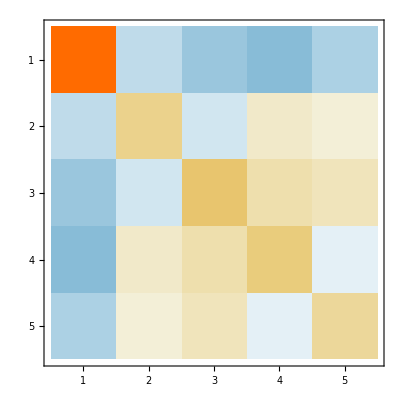

```mathematica
MatrixPlot[m]
```

```mathematica
vzz=l[["/5/0.5/0/spin_correlation/zz"]];
vpm=l[["/5/0.5/0/spin_correlation/pm"]];
vmp=l[["/5/0.5/0/spin_correlation/mp"]];
v=vzz+1/2(vpm+vmp)
```

{-0.00146386,-0.00173172,-0.00173172,-0.00146386}

```mathematica
imp=l[["/5/0.5/0/spin_correlation_imp/zz"]]+0.5(l[["/5/0.5/0/spin_correlation_imp/pm"]]+l[["/5/0.5/0/spin_correlation_imp/mp"]])
```

0.671385

```mathematica
m[[1]]
Prepend[v,imp]
%-%%
```

{0.671385,-0.00146386,-0.00173172,-0.00173172,-0.00146386}

{0.671385,-0.00146386,-0.00173172,-0.00173172,-0.00146386}

{0.,0.,0.,0.,0.}